```mathematica
data=RandomVariate[NormalDistribution[0,1],10]
```

{-0.806276,-0.195467,-1.76746,-0.0690425,-0.607029,0.126303,1.75037,0.807407,-1.99998,1.93376}

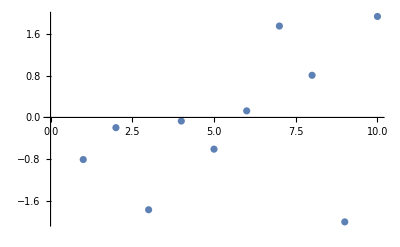

```mathematica
ListPlot[data]
```

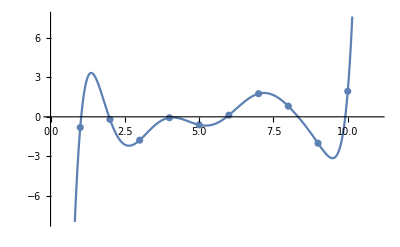

```mathematica
Fit[data,Table[x^p,{p,0,11}],x];
Show[Plot[%,{x,0,11}],ListPlot[data]]
```

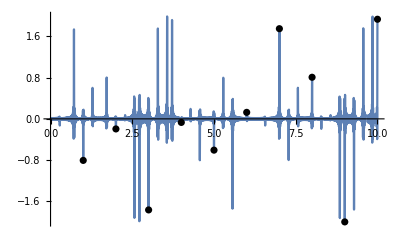

```mathematica
Fit[data,Table[Sin[p x],{p,1,500}],x, FitRegularization->{"Tikhonov",1}];
Show[Plot[{%},{x,0,10},PlotRange->All,PlotPoints->200],ListPlot[data, PlotStyle->Black]]
```

```mathematica
Sum[Coefficient[%214[[p]],Sin[p x]] 1/(p/10)^(.75)Sin[p x],{p,1,70}]
```

-0.0671771 Sin[x]+0.455066 Sin[2 x]-0.26391 Sin[3 x]+0.2821 Sin[4 x]-0.133935 Sin[5 x]+0.0323195 Sin[6 x]-0.118542 Sin[7 x]-0.0740492 Sin[8 x]+0.0428893 Sin[9 x]+0.00677106 Sin[10 x]+0.0948929 Sin[11 x]+0.0954607 Sin[12 x]-0.081797 Sin[13 x]-0.00387798 Sin[14 x]-0.104516 Sin[15 x]+0.0344733 Sin[16 x]-0.0508852 Sin[17 x]+0.0338222 Sin[18 x]+0.0116887 Sin[19 x]+0.031232 Sin[20 x]+0.00107679 Sin[21 x]+0.828739 Sin[22 x]-0.0141106 Sin[23 x]-0.0234024 Sin[24 x]-0.0115473 Sin[25 x]-0.0241457 Sin[26 x]+0.0449095 Sin[27 x]-0.0268566 Sin[28 x]+0.0682312 Sin[29 x]-0.00365521 Sin[30 x]+0.0413024 Sin[31 x]-0.0464628 Sin[32 x]-0.0440967 Sin[33 x]+0.00275129 Sin[34 x]-0.0167153 Sin[35 x]+0.0289348 Sin[36 x]+0.0364677 Sin[37 x]-0.0119071 Sin[38 x]+0.0270529 Sin[39 x]-0.0530064 Sin[40 x]+0.034014 Sin[41 x]-0.0479315 Sin[42 x]+0.00640104 Sin[43 x]+0.0632092 Sin[44 x]-0.00142808 Sin[45 x]+0.0411454 Sin[46 x]-0.0372125 Sin[47 x]+0.0405266 Sin[48 x]-0.0248517 Sin[49 x]+0.00395744 Sin[50 x]-0.0247433 Sin[51 x]-0.0139734 Sin[52 x]+0.00955236 Sin[53 x]+0.00645031 Sin[54 x]+0.0258815 Sin[55 x]+0.0295714 Sin[56 x]-0.0274758 Sin[57 x]-0.00503396 Sin[58 x]-0.0338373 Sin[59 x]+0.00988155 Sin[60 x]-0.0142881 Sin[61 x]+0.0142205 Sin[62 x]+0.00381069 Sin[63 x]+0.0148427 Sin[64 x]-0.00574625 Sin[65 x]+0.121742 Sin[66 x]-0.0117841 Sin[67 x]-0.00893794 Sin[68 x]-0.00649741 Sin[69 x]-0.0107535 Sin[70 x]

```mathematica
CoList=CoefficientList[%185,x]
```

{0,62.5959,0,-20807.,0,3.61087×10^6,0,-3.4158×10^8,0,1.93073×10^10,0,-7.14257×10^11,0,1.84715×10^13,0,-3.49807×10^14,0,5.01157×10^15,0,-5.54899×10^16,0,4.79585×10^17,0,-3.21404×10^18,0,1.5988×10^19,0,-4.88118×10^19,0,-3.69487×10^19,0,1.71989×10^21,0,-1.41484×10^22,0,8.03474×10^22,0,-3.66098×10^23,0,1.41238×10^24,0,-4.74117×10^24,0,1.40822×10^25,0,-3.74407×10^25,0,8.98846×10^25,0,-1.96196×10^26,0,3.91589×10^26,0,-7.18135×10^26,0,1.21517×10^27,0,-1.90427×10^27,0,2.77276×10^27,0,-3.76253×10^27,0,4.77096×10^27,0,-5.66714×10^27,0,6.32039×10^27,0,-6.63223×10^27}

```mathematica
RegList=Table[1/i^(.5)CoList[[i]] x^i//N,{i,1,70}]
```

{0.,44.262 x^2,0.,-10403.5 x^4,0.,1.47413×10^6 x^6,0.,-1.20767×10^8 x^8,0.,6.10551×10^9 x^10,0.,-2.06188×10^11 x^12,0.,4.93671×10^12 x^14,0.,-8.74518×10^13 x^16,0.,1.18124×10^15 x^18,0.,-1.24079×10^16 x^20,0.,1.02248×10^17 x^22,0.,-6.56063×10^17 x^24,0.,3.1355×10^18 x^26,0.,-9.22456×10^18 x^28,0.,-6.74588×10^18 x^30,0.,3.04037×10^20 x^32,0.,-2.42644×10^21 x^34,0.,1.33912×10^22 x^36,0.,-5.9389×10^22 x^38,0.,2.23317×10^23 x^40,0.,-7.31578×10^23 x^42,0.,2.12297×10^24 x^44,0.,-5.52033×10^24 x^46,0.,1.29737×10^25 x^48,0.,-2.77463×10^25 x^50,0.,5.43036×10^25 x^52,0.,-9.77259×10^25 x^54,0.,1.62384×10^26 x^56,0.,-2.50043×10^26 x^58,0.,3.57962×10^26 x^60,0.,-4.77841×10^26 x^62,0.,5.96369×10^26 x^64,0.,-6.97576×10^26 x^66,0.,7.6646×10^26 x^68,0.,-7.92703×10^26 x^70}

```mathematica
Sum[RegList[[j]],{j,1,70}]
```

0.+44.262 x^2-10403.5 x^4+1.47413×10^6 x^6-1.20767×10^8 x^8+6.10551×10^9 x^10-2.06188×10^11 x^12+4.93671×10^12 x^14-8.74518×10^13 x^16+1.18124×10^15 x^18-1.24079×10^16 x^20+1.02248×10^17 x^22-6.56063×10^17 x^24+3.1355×10^18 x^26-9.22456×10^18 x^28-6.74588×10^18 x^30+3.04037×10^20 x^32-2.42644×10^21 x^34+1.33912×10^22 x^36-5.9389×10^22 x^38+2.23317×10^23 x^40-7.31578×10^23 x^42+2.12297×10^24 x^44-5.52033×10^24 x^46+1.29737×10^25 x^48-2.77463×10^25 x^50+5.43036×10^25 x^52-9.77259×10^25 x^54+1.62384×10^26 x^56-2.50043×10^26 x^58+3.57962×10^26 x^60-4.77841×10^26 x^62+5.96369×10^26 x^64-6.97576×10^26 x^66+7.6646×10^26 x^68-7.92703×10^26 x^70

```mathematica
1000-40
%*(1+0.05/12)
```

960

964.

```mathematica
(%-40)*(1+0.05/12)
```

13.5853

```mathematica
500*(1+0.05/12)
```

502.083

```mathematica
5/12.
```

0.416667